# FES - Ficha 3

## Problema 1. Alínea a)

```mathematica
Clear["Global"]
```

```mathematica
me= 9.10938356×10^(-31);
h = 1.0545718×10^(-34);
sigma = 1.058*10^(-10);
conv= h^2/(me*sigma^2);
q= 6.24150913×10^(18);
c=3.83;
```

```mathematica
Einf = Table[conv/2*(i^2-2*c),{i,1,7}]*q
```

{-22.6687,-12.4576,4.56096,28.3869,59.0202,96.4609,140.709}

```mathematica
Enat = Table[1/2*(i^2-2*c),{i,1,7}]
```

{-3.33,-1.83,0.67,4.17,8.67,14.17,20.67}

## Problema 1. Alínea c)

Potencial:

```mathematica
v[x_] = If[Abs[x]> Pi/2, 0, c*(Sin[x]^4 - 1)];
```

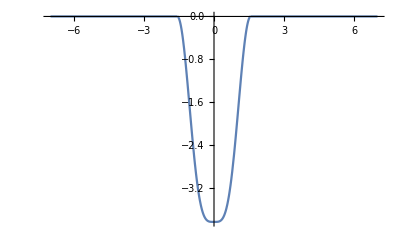

```mathematica
xmax = 7;
Plot[v[x],{x,-xmax,xmax},PlotRange->All]
```

Estado Fundamental -- Condições iniciais pares

Eigenvalue de Energia, na precisão pedida:

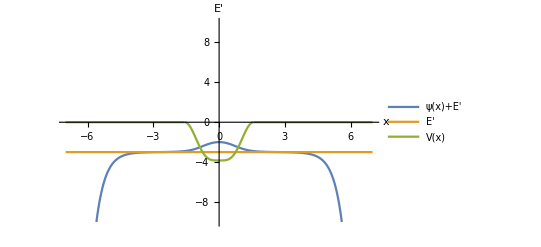

```mathematica
eig0=-2.993;

sol =NDSolve[{ - y''[x]/2+v[x] y[x]==eig0 y[x],y[0]==1,y'[0]==0},y,{x,-xmax,xmax}];
g[x_]=First[Evaluate[y[x]/.sol]];
Plot[{eig0+g[x],eig0,v[x]},{x,-xmax,xmax},PlotRange->{-10,10},AxesLabel->{"x","E'"},PlotLegends->{"ψ(x)+E'","E'","V(x)"}]
```

Tentativas em outros eigenvalues

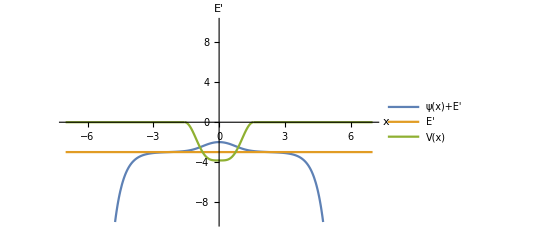

```mathematica
eig01=-2.992;

sol =NDSolve[{ - y''[x]/2+v[x] y[x]==eig01 y[x],y[0]==1,y'[0]==0},y,{x,-xmax,xmax}];
g[x_]=First[Evaluate[y[x]/.sol]];
Plot[{eig01+g[x],eig01,v[x]},{x,-xmax,xmax},PlotRange->{-10,10},AxesLabel->{"x","E'"},PlotLegends->{"ψ(x)+E'","E'","V(x)"}]
```

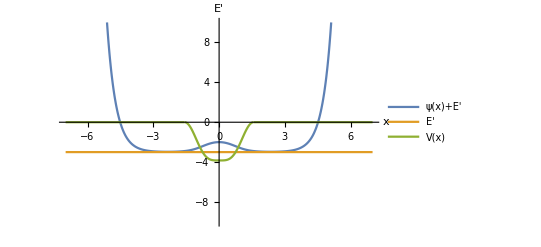

```mathematica
eig02=-2.994;

sol =NDSolve[{ - y''[x]/2+v[x] y[x]==eig02 y[x],y[0]==1,y'[0]==0},y,{x,-xmax,xmax}];
g[x_]=First[Evaluate[y[x]/.sol]];
Plot[{eig02+g[x],eig02,v[x]},{x,-xmax,xmax},PlotRange->{-10,10},AxesLabel->{"x","E'"},PlotLegends->{"ψ(x)+E'","E'","V(x)"}]
```

1.ba Estado Excitado -- Condições iniciais ímpares

Eigenvalue de Energia, na precisão pedida:

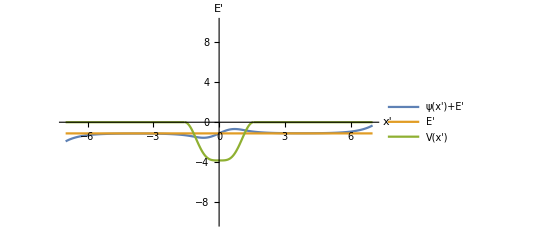

```mathematica
eig1=-1.120;
sol =NDSolve[{ - y''[x]/2+v[x] y[x]==eig1 y[x],y[0]==0,y'[0]==1},y,{x,-xmax,xmax}];
g[x_]=First[Evaluate[y[x]/.sol]];
Plot[{eig1+g[x],eig1,v[x]},{x,-xmax,xmax},PlotRange->{-10,10},AxesLabel->{"x'","E'"},PlotLegends->{"ψ(x')+E'","E'","V(x')"}]
```

Tentativas em outros eigenvalues

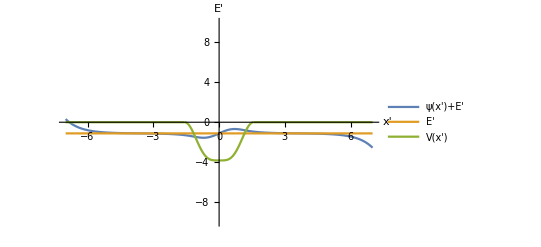

```mathematica
eig11=-1.119;

sol =NDSolve[{ - y''[x]/2+v[x] y[x]==eig11 y[x],y[0]==0,y'[0]==1},y,{x,-xmax,xmax}];
g[x_]=First[Evaluate[y[x]/.sol]];
Plot[{eig11+g[x],eig11,v[x]},{x,-xmax,xmax},PlotRange->{-10,10},AxesLabel->{"x'","E'"},PlotLegends->{"ψ(x')+E'","E'","V(x')"}]
```

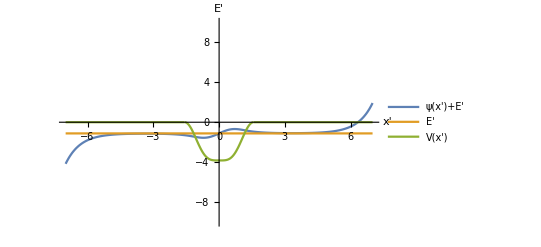

```mathematica
eig12=-1.121;

sol =NDSolve[{ - y''[x]/2+v[x] y[x]==eig12 y[x],y[0]==0,y'[0]==1},y,{x,-xmax,xmax}];
g[x_]=First[Evaluate[y[x]/.sol]];
Plot[{eig12+g[x],eig12,v[x]},{x,-xmax,xmax},PlotRange->{-10,10},AxesLabel->{"x'","E'"},PlotLegends->{"ψ(x')+E'","E'","V(x')"}]
```

#### Método mais preciso do Cálculo de Valores próprios de Energia, fazendo um shift nas energias de forma a que o mínimo do potencial coincida com o zero da escala:

```mathematica
V1[x_]:=If[Abs[x]> Pi/2, 0,c*(Sin[x]^4 - 1)]+c
ℒ=-u''[x]/2+V1[x]*u[x];
```

Resolver equação impondo que função de onda se anule em x=100 e x=-100

```mathematica
{energies,wavefunctions}=NDEigensystem[ℒ,u[x],{x,-100,100},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[«1»] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

3  Primeiros Valores próprios de energia:

```mathematica
energies-c
```

{-2.99314,-1.11964,0.000121388,0.00110436,0.0014124,0.00315664,0.00618228,0.00987655,0.0125921,0.0148993}

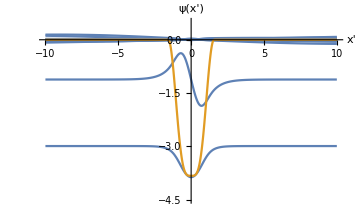

```mathematica
Show[Plot[{Evaluate[-wavefunctions+energies]-c,V1[x]-c},{x,-10,10}],PlotRange->{{-10,10},{-4.5,0.5}},AxesOrigin->{0,0},ImageSize->Medium,AxesLabel->{"x'","ψ(x')"}]
```

Energias dos estados ligados em eV

```mathematica
E0 =q*conv*(-2.9931421631303863)
E1 =q*conv*(-1.1196434030546212)
```

-20.3755

-7.62187

```mathematica
q*conv*-2.993
```

-20.3746

```mathematica
q*conv*-1.120
```

-7.62429

## Problema 2.

Recorrendo ao método da bisseção “manual” determinaram-se os limites das 3 primeiras bandas com a precisão pedida:

```mathematica
Eb1Max=-2.9541;
Eb1Min = -3.0328;
Eb2Max=-0.7774;
Eb2Min =-1.3515;
Eb3Min = 0.2909;
Eb3Max =2.0873;
```

Em eV:

```mathematica
Eb1MaxeV=-2.9541*q*conv
Eb1MineV = -3.0328*q*conv
Eb2MaxeV= -0.7774*q*conv
Eb2MineV =-1.3515*q*conv
Eb3MineV = 0.2909*q*conv
Eb3MaxeV =2.0873*q*conv
```

-20.1098

-20.6455

-5.29208

-9.20021

1.98027

14.2091

### 1.aa Banda

```mathematica
dt = Pi/8;
tmax = 2^10 Pi;
V[x_,c_] := c(Sin[x]^4-1);
f[x_]=Integrate[xt (1-xt),{xt,0,x}]/Integrate[xt (1-xt),{xt,0,1}];
En=Eb1Min + f/@Range[0,1,0.01] *(Eb1Max-Eb1Min);
```

```mathematica
Clear@u
sols =NDSolve[{u''[x]/2 + (#-V[x,c]) u[x] == 0, u[0] == 1,u'[0]==0},{u},{x,0,tmax}]&/@En;
```

```mathematica
Plot[Evaluate[u[x] /. sols], {x,0,60},PlotRange->{-1,1}, PlotStyle-> Automatic,AxesLabel->{"x'","ψ(x')"}]
```

-Graphics-

```mathematica
positions =((u[x] /. sols)/.x->#&)/@Range[dt,tmax ,dt];
FFT = Fourier/@Transpose[positions[[All,All,1]]];
```

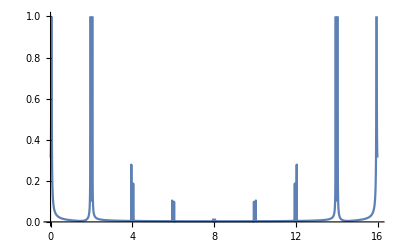

```mathematica
ListLinePlot[Transpose[{Range[0,2Pi/dt-2Pi/tmax,2Pi/tmax],Abs/@#}]&/@{FFT[[5]]},PlotRange->{0,1}]
```

```mathematica
dataPeaks=Abs/@FFT;
```

```mathematica
peaks=Drop[MaxDetect[#],1]&/@dataPeaks
```

{1}
 |  |  |  |

```mathematica
prevMax=1;
kList= N@2Pi/tmax(Table[prevMax+=-1+(Position[peaks[[i,prevMax;;]],1][[1,1]]),{i,1,Length@peaks}   ]);
```

1.aa Banda

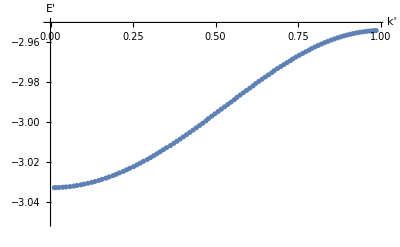

```mathematica
ListPlot[Transpose@{kList,En},PlotRange->{-3.05,-2.95},AxesLabel->{"k'","E'"}]
```

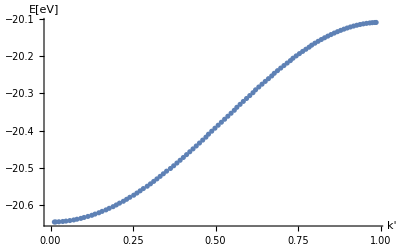

```mathematica
ListPlot[Transpose@{kList,q*conv*En},AxesLabel->{"k'","E[eV]"}]
```

```mathematica
Export["energyBand1.png",%,ImageSize->700]
```

energyBand1.png

### 2.aa Banda

```mathematica
En2=Eb2Min + f/@Range[0,1,0.01] *(Eb2Max-Eb2Min);
```

```mathematica
Clear@u
sols =NDSolve[{u''[x]/2 + (#-V[x,c]) u[x] == 0, u[0] == 1,u'[0]==0},{u},{x,0,tmax}]&/@En2;
```

```mathematica
(*Plot[Evaluate[u[x] /. sols], {x,0,tmax},PlotRange->{-100,100}, PlotStyle-> Automatic]*)
```

```mathematica
positions =((u[x] /. sols)/.x->#&)/@Range[dt,tmax ,dt];
FFT = Fourier/@Transpose[positions[[All,All,1]]];
```

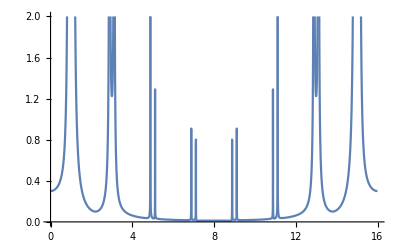

```mathematica
ListLinePlot[Transpose@{Range[0,2Pi/dt-2Pi/tmax,2Pi/tmax],Abs@FFT[[10]]},PlotRange->{0,2}]
```

```mathematica
dataPeaks=Abs/@FFT;
```

```mathematica
peaks=Drop[MaxDetect[#],1]&/@dataPeaks
```

{1}
 |  |  |  |

```mathematica
prevMax=520;
kList2= N@2Pi/tmax(Table[prevMax+=1-(Position[Reverse@peaks[[i,1;;prevMax]],1][[1,1]]),{i,1,Length@peaks}   ]);
```

2.aa Banda

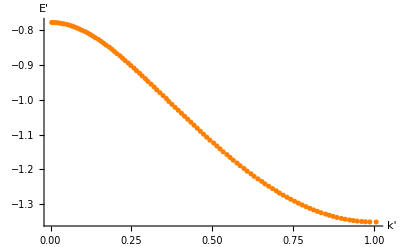

```mathematica
ListPlot[Transpose/@{{kList2,En2}},PlotRange->Automatic,AxesLabel->{"k'","E'"},PlotStyle->Orange]
```

2.aa Banda em eV

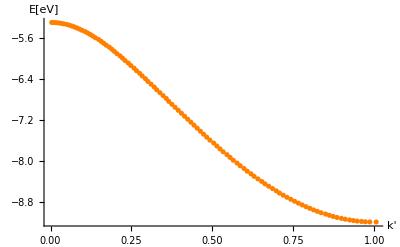

```mathematica
ListPlot[Transpose/@{{kList2,q*conv*En2}},PlotRange->Automatic,AxesLabel->{"k'","E[eV]"},PlotStyle->Orange]
```

1.aa e 2.aa Bandas [eV]

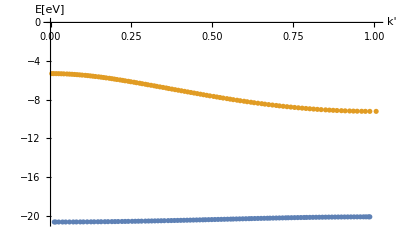

```mathematica
ListPlot[Transpose/@{{kList,q*conv*En},{kList2,q*conv*En2}},PlotRange->All,AxesLabel->{"k'","E[eV]"}]
```

### 3.aa Banda

```mathematica
En3=Eb3Min + f/@Range[0,1,0.01] *(Eb3Max-Eb3Min);
Clear@u
sols =NDSolve[{u''[x]/2 + (#-V[x,c]) u[x] == 0, u[0] == 1,u'[0]==0},{u},{x,0,tmax}]&/@En3;
```

```mathematica
positions =((u[x] /. sols)/.x->#&)/@Range[dt,tmax ,dt];
FFT = Fourier/@Transpose[positions[[All,All,1]]];
```

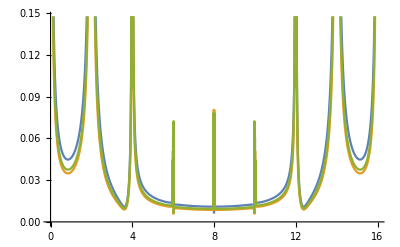

```mathematica
ListLinePlot[Transpose@{Range[0,2Pi/dt-2Pi/tmax,2Pi/tmax],Abs/@#}&/@FFT[[1;;3]]]
```

```mathematica
dataPeaks=Abs/@FFT;
```

```mathematica
peaks=Drop[MaxDetect[#],1]&/@dataPeaks
```

{1}
 |  |  |  |

```mathematica
prevMax=1;
kList3= N@2Pi/tmax(Table[prevMax+=-1+(Position[peaks[[i,prevMax;;]],1][[1,1]]),{i,1,Length@peaks}   ]);
```

3.aa Banda

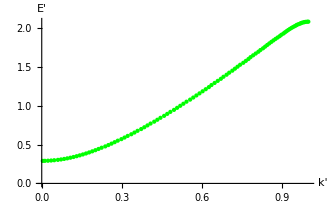

```mathematica
ListPlot[Transpose/@{{kList3,En3}},PlotRange->Automatic,AxesLabel->{"k'","E'"},PlotStyle->Green]
```

3.aa Banda [eV]

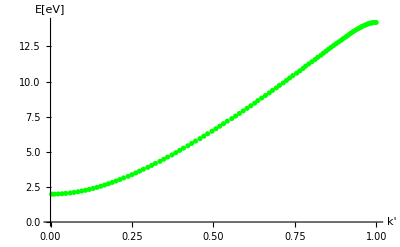

```mathematica
ListPlot[Transpose/@{{kList3,q*conv*En3}},PlotRange->Automatic,AxesLabel->{"k'","E[eV]"},PlotStyle->Green]
```

1.aa + 2.aa + 3.aa Bandas [eV]

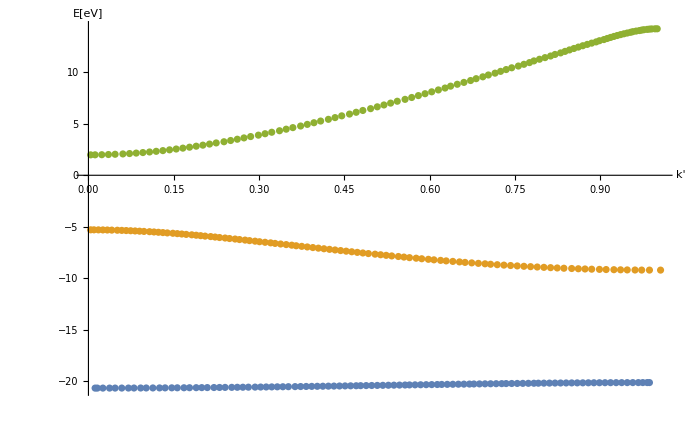

```mathematica
ListPlot[Transpose/@{{kList,q*conv*En},{kList2,q*conv*En2},{kList3,q*conv*En3}},PlotRange->Automatic,AxesLabel->{"k'","E[eV]"}]
```

## Problema 3.

```mathematica
FourierSeries[V[x,c],x,10]
u[n_]:=FourierCoefficient[V[x,c],x,2 n]
kin[k_,n_]:=0.5*(k+2n)^2
```

-2.39375-0.9575 ⅇ^(-2 ⅈ x)-0.9575 ⅇ^(2 ⅈ x)+0.239375 ⅇ^(-4 ⅈ x)+0.239375 ⅇ^(4 ⅈ x)

k’=0

```mathematica
k=0.0;
m=({{kin[k,-3]+u[0], u[1], u[2], 0, 0, 0, 0}, {u[-1], kin[k,-2]+u[0], u[1], u[2], 0, 0, 0}, {u[-2], u[-1], kin[k,-1]+u[0], u[1], u[2], 0, 0}, {0, u[-2], u[-1], kin[k,0]+u[0], u[1], u[2], 0}, {0, 0, u[-2], u[-1], kin[k,1]+u[0], u[1], u[2]}, {0, 0, 0, u[-2], u[-1], kin[k,2]+u[0], u[1]}, {0, 0, 0, 0, u[-2], u[-1], kin[k,3]+u[0]}});
Sort[Eigenvalues[N[m]]]
```

{-3.03282,-0.77731,0.290941,5.65293,5.70209,15.7038,15.7042}

Energias das Bandas em eV

```mathematica
Energies0 = q*conv*{-3.032818846170643,-0.7773095091992758,0.2909412065809056,5.6529291130735,5.7020895174143345,15.703755396125775,15.704163122175403}
```

{-20.6456,-5.29146,1.98055,38.4818,38.8164,106.902,106.905}

k’ = 0.5

```mathematica
k=0.5;
m=({{kin[k,-3]+u[0], u[1], u[2], 0, 0, 0, 0}, {u[-1], kin[k,-2]+u[0], u[1], u[2], 0, 0, 0}, {u[-2], u[-1], kin[k,-1]+u[0], u[1], u[2], 0, 0}, {0, u[-2], u[-1], kin[k,0]+u[0], u[1], u[2], 0}, {0, 0, u[-2], u[-1], kin[k,1]+u[0], u[1], u[2]}, {0, 0, 0, u[-2], u[-1], kin[k,2]+u[0], u[1]}, {0, 0, 0, 0, u[-2], u[-1], kin[k,3]+u[0]}});
Sort[Eigenvalues[N[m]]]
```

{-2.99563,-1.12182,0.95935,3.83094,7.78584,12.8403,18.8198}

Energias das Bandas em eV

```mathematica
Energies1 = q*conv*{-2.995633021281117,-1.1218239825125802,0.9593499942877797,3.830935444749082,7.7858415195857855,12.840317844604758,18.819762200566288}
```

{-20.3925,-7.63671,6.53068,26.0787,53.0014,87.4092,128.114}

k’ = 1.

```mathematica
k=1.;
m=({{kin[k,-3]+u[0], u[1], u[2], 0, 0, 0, 0}, {u[-1], kin[k,-2]+u[0], u[1], u[2], 0, 0, 0}, {u[-2], u[-1], kin[k,-1]+u[0], u[1], u[2], 0, 0}, {0, u[-2], u[-1], kin[k,0]+u[0], u[1], u[2], 0}, {0, 0, u[-2], u[-1], kin[k,1]+u[0], u[1], u[2]}, {0, 0, 0, u[-2], u[-1], kin[k,2]+u[0], u[1]}, {0, 0, 0, 0, u[-2], u[-1], kin[k,3]+u[0]}});
Sort[Eigenvalues[N[m]]]
```

{-2.95403,-1.35143,2.08768,2.39506,10.1495,10.2298,22.1872}

Energias das Bandas em eV

```mathematica
Energies2 = q*conv*{-2.9540278616896476,-1.3514275608786377,2.0876764352313453,2.3950592473836028,10.149509033568123,10.22980327356334,22.187157432821863}
```

{-20.1093,-9.19971,14.2117,16.3041,69.0918,69.6384,151.037}

### Alínea c)

```mathematica
SMat = 7;
mV =SparseArray[{Band[{1,1}]->(Table[N[kin[k,i]+u[0]],{i,-(SMat-1)/2,(SMat-1)/2,1}]),Band[{2,1}]->u[-1],Band[{1,2}]->u[1],Band[{3,1}]->u[-2],Band[{1,3}]->u[2]},{SMat,SMat}]
```

SparseArray[…]

```mathematica
GetEigVal[k1_,SMat_]:= {d =SparseArray[{Band[{1,1}]->(Table[N[kin[k1,i]+u[0]],{i,-(SMat-1)/2,(SMat-1)/2,1}]),Band[{2,1}]->u[-1],Band[{1,2}]->u[1],Band[{3,1}]->u[-2],Band[{1,3}]->u[2]},{SMat,SMat}]; Sort[Eigenvalues[N[d]]]}
```

```mathematica
Final = Table[First@GetEigVal[i,SMat] , {i,0,1,0.01}];
```

```mathematica
Finall=Transpose[Final];
```

Todas as primeiras 7 (dimensão da matriz) bandas

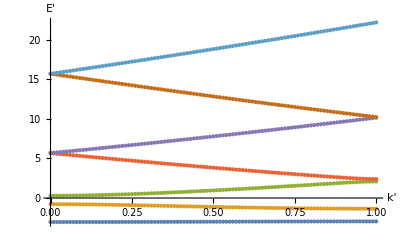

```mathematica
ListPlot[Transpose[{Range[0,1,0.01],#}]&/@ Finall,AxesLabel->{"k'","E'"}]
```

1.aa + 2.aa + 3.aa Bandas

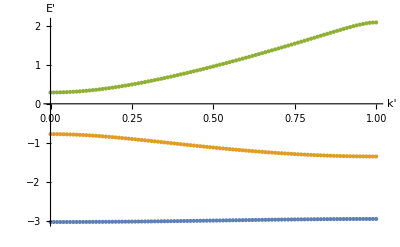

```mathematica
ListPlot[Transpose[{Range[0,1,0.01],#}]&/@ Finall[[1;;3]],AxesLabel->{"k'","E'"}]
```

1.aa + 2.aa + 3.aa Bandas em eV

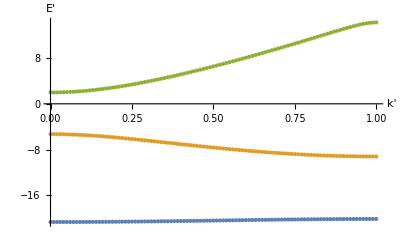

```mathematica
ListPlot[Transpose[{Range[0,1,0.01],#}]&/@ (q*conv*Finall[[1;;3]]),AxesLabel->{"k'","E'"}]
```

1.aa Zona de Brillouin Completa

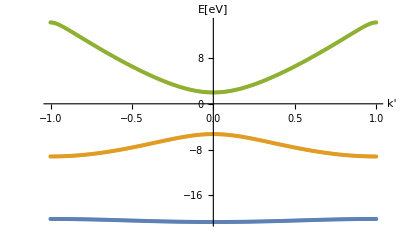

```mathematica
k =Reverse[#]&/@Finall[[1;;3]];
Drop[#,-1]&/@k[[1;;3]];
Final3 = Join[Drop[#,-1]&/@k[[1;;3]],Finall[[1;;3]],2];
ListPlot[Transpose[{Range[-1,1,0.01],#}]&/@(q*conv*Final3),AxesLabel->{"k'","E[eV]"}]
```

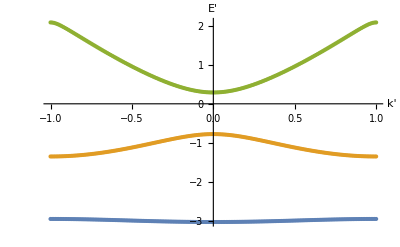

```mathematica
ListPlot[Transpose[{Range[-1,1,0.01],#}]&/@(Final3),AxesLabel->{"k'","E'"}]
```

### Cálculo das energias para os ks estimados na alínea b)

1.aa Banda

```mathematica
Final1 = First@GetEigVal[#,SMat]&/@kList ;
Finall1=Transpose[Final1];
```

```mathematica
Finall1;
```

2.aa Banda

```mathematica
Final2 = First@GetEigVal[#,SMat]&/@kList2 ;
Finall2=Transpose[Final2];
```

3.aa Banda

```mathematica
Finall3 = First@GetEigVal[#,SMat]&/@kList3;
Finalll3=Transpose[Finall3];
```

### Comparação com problema anterior

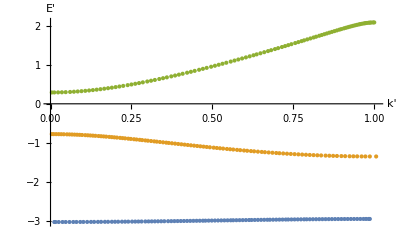

```mathematica
Show[ListPlot[Transpose/@{{kList,Finall1[[1]]},{kList2,Finall2[[2]]},{kList3,Finalll3[[3]]}}],ListPlot[Transpose/@{{kList,En},{kList2,En2},{kList3,En3}},PlotStyle->{Opacity[0.1],Opacity[0.1],Opacity[0.1]}],AxesLabel->{"k'","E'"}]
```

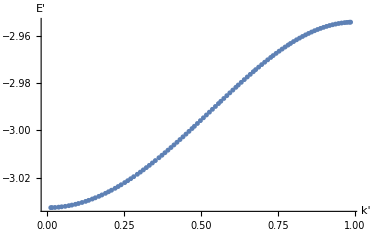

```mathematica
Show[ListPlot[Transpose/@{{kList,Finall1[[1]]}}],ListPlot[Transpose/@{{kList,En}},PlotStyle->{Opacity[0.3],Blue}],AxesLabel->{"k'","E'"}]
```

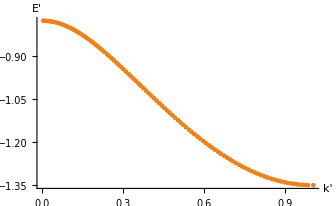

```mathematica
Show[ListPlot[Transpose/@{{kList2,Finall2[[2]]}}],ListPlot[Transpose/@{{kList2,En2}},PlotStyle->{Orange,Red}],AxesLabel->{"k'","E'"}]
```

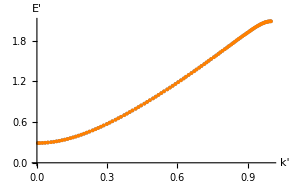

```mathematica
Show[ListPlot[Transpose/@{{kList3,Finalll3[[3]]}}],ListPlot[Transpose/@{{kList3,En3}},PlotStyle->{Orange,Red}],AxesLabel->{"k'","E'"}]
```

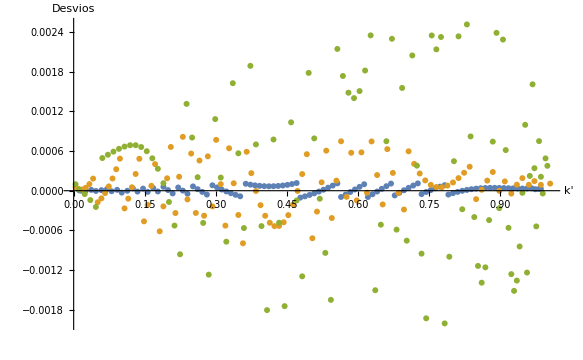

```mathematica
ListPlot[Transpose/@{{kList,(Finall1[[1]]-En)},{kList2,(Finall2[[2]]-En2)},{kList3,(Finalll3[[3]]-En3)}},PlotRange->Full,AxesLabel->{"k'","Desvios"}]
```

## Estudo Extra

```mathematica
Estudo= Table[{i,First@First@GetEigVal[kList[[10]],i]-En[[10]]} , {i,3,29,2}];
```

```mathematica
Estudo
```

{{3,0.0018931},{5,0.000421367},{7,-0.000028506},{9,-0.0000303732},{11,-0.0000303914},{13,-0.0000303915},{15,-0.0000303915},{17,-0.0000303915},{19,-0.0000303915},{21,-0.0000303915},{23,-0.0000303915},{25,-0.0000303915},{27,-0.0000303915},{29,-0.0000303915}}

```mathematica
Estudo2= Table[{i,(First@GetEigVal[kList2[[-10]],i])[[2]]-En2[[-10]]} , {i,3,29,2}];
```

```mathematica
Estudo3= Table[{i,(First@GetEigVal[kList3[[10]],i])[[3]]-En3[[10]]} , {i,3,29,2}];
```

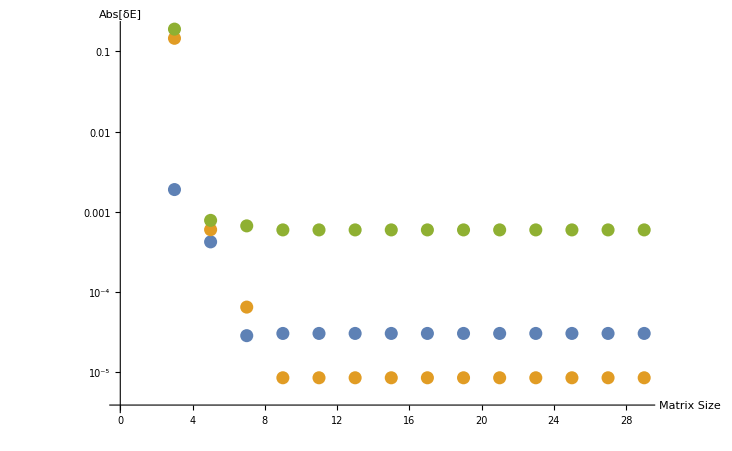

```mathematica
ListLogPlot[Abs/@{Estudo,Estudo2,Estudo3},AxesLabel->{"Matrix Size","Abs[δE]"}]
```

```mathematica
kList2[[-10]]
```

0.0742188

```mathematica
kList3[[10]]
```

0.107422

```mathematica
kList[[10]]
```

0.101563

```mathematica
(*Table[{i,kList[[j]]  ,First@First@GetEigVal[kList[[j]],i]-En[[j]]} , {i,3,29,2},{j,1,Length@En,10}]*)
```

```mathematica
Estudo3D={{{3,0.01171875,0.0016896026859400948},{3,0.11328125,0.0019796660248831977},{3,0.220703125,0.0029072274283357125},{3,0.322265625,0.004313622652845073},{3,0.421875,0.006591068336252448},{3,0.517578125,0.009534235911091038},{3,0.61328125,0.013807604309277188},{3,0.70703125,0.019196612000756286},{3,0.80078125,0.026166175840337313},{3,0.8984375,0.035515946684478994},{3,0.986328125,0.04562375661643925}},{{5,0.01171875,0.00045258187029872943},{5,0.11328125,0.00044914108203952807},{5,0.220703125,0.000507104167946526},{5,0.322265625,0.000459094045965891},{5,0.421875,0.0005514811468425584},{5,0.517578125,0.00048322554237767434},{5,0.61328125,0.0006042083765693818},{5,0.70703125,0.0005535951536765893},{5,0.80078125,0.00046698540692657886},{5,0.8984375,0.000525008984836095},{5,0.986328125,0.0004779310961202654}},{{7,0.01171875,5.101243833127711*^-6},{7,0.11328125,-1.3177581932311*^-6},{7,0.220703125,0.0000485400375223044},{7,0.322265625,-0.000010970132103160779},{7,0.421875,0.0000679679276367473},{7,0.517578125,-0.0000131761791690721},{7,0.61328125,0.00009776763723934323},{7,0.70703125,0.00004353609410800985},{7,0.80078125,-0.00003666170954153003},{7,0.8984375,0.00004270144498796924},{7,0.986328125,0.000030063885771092203}},{{9,0.01171875,3.378248223828706*^-6},{9,0.11328125,-3.2211241527413392*^-6},{9,0.220703125,0.00004609912552266948},{9,0.322265625,-0.000014319952657881885},{9,0.421875,0.00006323153558618344},{9,0.517578125,-0.0000198601327925374},{9,0.61328125,0.0000883380558862612},{9,0.70703125,0.000030419681305904334},{9,0.80078125,-0.00005468970251820693},{9,0.8984375,0.00001801634674825081},{9,0.986328125,-2.1117486559418808*^-6}},{{11,0.01171875,3.3600758011509413*^-6},{11,0.11328125,-3.239292355683432*^-6},{11,0.220703125,0.00004608100631875445},{11,0.322265625,-0.000014337888212700989},{11,0.421875,0.00006321405527121016},{11,0.517578125,-0.000019876745233293747},{11,0.61328125,0.00008832291703342321},{11,0.70703125,0.00003040671312026788},{11,0.80078125,-0.000054699763385901434},{11,0.8984375,0.000018009853465894565},{11,0.986328125,-2.115112348377579*^-6}},{{13,0.01171875,3.360002320818012*^-6},{13,0.11328125,-3.239372674990193*^-6},{13,0.220703125,0.0000460809056468392},{13,0.322265625,-0.00001433802336903156},{13,0.421875,0.00006321386735308465},{13,0.517578125,-0.000019877007602531194},{13,0.61328125,0.00008832254921653515},{13,0.70703125,0.000030406202764510226},{13,0.80078125,-0.000054700465054402514},{13,0.8984375,0.000018008890109388886},{13,0.986328125,-2.116373124749771*^-6}},{{15,0.01171875,3.3600021742685726*^-6},{15,0.11328125,-3.2393727926738336*^-6},{15,0.220703125,0.000046080905519829685},{15,0.322265625,-0.000014338023469839811},{15,0.421875,0.00006321386724117417},{15,0.517578125,-0.00001987700767802636},{15,0.61328125,0.00008832254917034987},{15,0.70703125,0.00003040620276228978},{15,0.80078125,-0.00005470046505573478},{15,0.8984375,0.000018008890098286656},{15,0.986328125,-2.1163732091267207*^-6}},{{17,0.01171875,3.3600021760449295*^-6},{17,0.11328125,-3.2393728131019373*^-6},{17,0.220703125,0.000046080905518941506},{17,0.322265625,-0.000014338023479609774},{17,0.421875,0.00006321386725449685},{17,0.517578125,-0.000019877007686019965},{17,0.61328125,0.00008832254915569493},{17,0.70703125,0.00003040620271654859},{17,0.80078125,-0.00005470046510058779},{17,0.8984375,0.000018008890070309036},{17,0.986328125,-2.1163732513151956*^-6}},{{19,0.01171875,3.360002176933108*^-6},{19,0.11328125,-3.2393728259805243*^-6},{19,0.220703125,0.000046080905542922324},{19,0.322265625,-0.000014338023490712004},{19,0.421875,0.00006321386728824763},{19,0.517578125,-0.00001987700768246725},{19,0.61328125,0.00008832254922364058},{19,0.70703125,0.000030406202724542197},{19,0.80078125,-0.00005470046506905746},{19,0.8984375,0.000018008890095178032},{19,0.986328125,-2.116373239324787*^-6}},{{21,0.01171875,3.3600021756008402*^-6},{21,0.11328125,-3.239372795782458*^-6},{21,0.220703125,0.0000460809054820821},{21,0.322265625,-0.000014338023482274309},{21,0.421875,0.00006321386726737543},{21,0.517578125,-0.00001987700763317335},{21,0.61328125,0.00008832254915214222},{21,0.70703125,0.000030406202771171564},{21,0.80078125,-0.00005470046504951753},{21,0.8984375,0.000018008890036558256},{21,0.986328125,-2.1163732530915524*^-6}},{{23,0.01171875,3.3600021978053007*^-6},{23,0.11328125,-3.239372803776064*^-6},{23,0.220703125,0.00004608090550473065},{23,0.322265625,-0.000014338023474280703},{23,0.421875,0.00006321386721008793},{23,0.517578125,-0.000019877007743751562},{23,0.61328125,0.00008832254919077798},{23,0.70703125,0.000030406202702337737},{23,0.80078125,-0.00005470046505573478},{23,0.8984375,0.000018008890055654092},{23,0.986328125,-2.116373262861515*^-6}},{{25,0.01171875,3.3600021507318445*^-6},{25,0.11328125,-3.239372867280821*^-6},{25,0.220703125,0.000046080905530487826},{25,0.322265625,-0.00001433802345962576},{25,0.421875,0.00006321386728869172},{25,0.517578125,-0.00001987700769934264},{25,0.61328125,0.00008832254919699523},{25,0.70703125,0.00003040620276761885},{25,0.80078125,-0.00005470046510103188},{25,0.8984375,0.00001800889008496398},{25,0.986328125,-2.116373176264119*^-6}},{{27,0.01171875,3.3600022160129583*^-6},{27,0.11328125,-3.239372804220153*^-6},{27,0.220703125,0.00004608090552160604},{27,0.322265625,-0.000014338023284210522},{27,0.421875,0.00006321386714303046},{27,0.517578125,-0.00001987700766736822},{27,0.61328125,0.00008832254917257032},{27,0.70703125,0.000030406202578880936},{27,0.80078125,-0.00005470046508593285},{27,0.8984375,0.00001800889019198948},{27,0.986328125,-2.1163733352480563*^-6}},{{29,0.01171875,3.3600022284474562*^-6},{29,0.11328125,-3.2393729005875116*^-6},{29,0.220703125,0.000046080905407475115},{29,0.322265625,-0.000014338023379245612},{29,0.421875,0.00006321386719410071},{29,0.517578125,-0.000019877007679358627},{29,0.61328125,0.0000883225491774553},{29,0.70703125,0.000030406202697452756},{29,0.80078125,-0.000054700465110357754},{29,0.8984375,0.000018008890054765914},{29,0.986328125,-2.116373241989322*^-6}}};
```

```mathematica
ListPlot3D[MapAt[Log10[Abs[#]]&,Evaluate[Flatten[Estudo3D,1]],{All,3}],AxesLabel->{"Matrix Size","k","Log[Abs[δE]]"},PlotRange->{{3,30},All,All}]
```

-Graphics3D-